9.8 θ[t]+θ'[t]+θ''[t]==0.5 Sin[2 t]

9.8 θ[t]+θ'[t]+θ''[t]==0

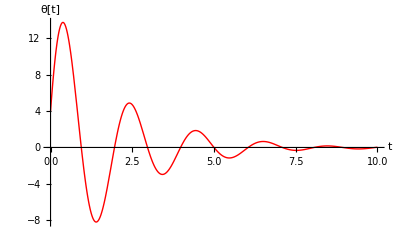

```mathematica
(*Example Problem*)
(*Solve the inhomogeneous diff eq through the techniques of variation of parameters:θ''[t]+ g/l *θ[t]+q  θ'[t]==Fd Sin[omg * t]*)

(*Define the inhomogeneous diff eq*)
l=1;g=9.8;omg=2;q=1;Fd=0.5;
f[t_]:=Fd Sin[omg * t]
inhomoeq=θ''[t]+ g/l *θ[t]+q  θ'[t]==f[t]
homoeq=θ''[t]+ g/l *θ[t]+q  θ'[t]==0
(*Get general sol of homo eq*)
yh=DSolve[homoeq,θ[t],t];
yh=θ[t]/.yh[[1]];
(*Get linearly independent sols of homo eq from its general sol*)
y1=yh/.{C[1]->1,C[2]->0};
y2=yh/.{C[1]->0,C[2]->1};
(*Get rEADY FOR GETTING PARTICULAR SOL OF INHOMOGENEOUS EQ*)
(*fIRST OF ALL FIND Wronskian Determinant*)
wrons=Det[{{y1,y2},{D[y1,t],D[y2,t]}}];
(*Now get particular sol*)
yp=-y1*Integrate[y2*f[t]/wrons,t]+y2*Integrate[y1*f[t]/wrons,t];
(*Now the general sol of inhomogeneous diff eq*)
ygen=(yh+yp)//Simplify;
algeq={(ygen/.t->0)==4,(ygen/.t->5)==0};
eq=Solve[algeq,{C[1],C[2]}];
ygen=ygen/.eq[[1]];
Plot[ygen,{t,0,10},AxesLabel->{"t","θ[t]"},PlotStyle->{{Red,Thick}},PlotRange->All]
```